# q q^-→ g g

## Feynman diagram

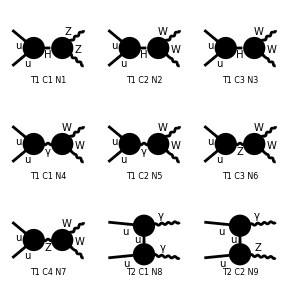

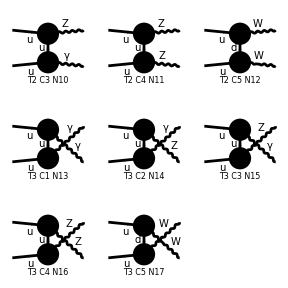

```mathematica
R1=CreateTopologies[0, 2 -> 2];
Diagrams=InsertFields[R1,{-F[3,{1}],F[3,{1}]}->{ V{5},V{5} },InsertionLevel->{Classes}];
Paint[%];
```

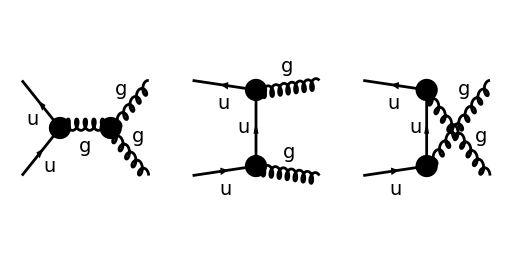

```mathematica
T1=CreateTopologies[0, 2 -> 2];
diagsG = InsertFields[T1, {-F[3, {1}], F[3, {1}]} ->
		{V{5},V{5}}, InsertionLevel -> {Classes},
		Model -> "SMQCD", ExcludeParticles -> {S[1], S[2], V[1],V[2],V[3]}];
Paint[diagsG, ColumnsXRows -> {3, 1}, Numbering -> None,SheetHeader->None,ImageSize->{512,256}];
```

## Square Amplitude (Mandelstam)

```mathematica
QQbar =FCFAConvert[CreateFeynAmp[diagsG,Truncated -> False],IncomingMomenta->{p,p'},OutgoingMomenta->{k,k'},
DropSumOver->True,ChangeDimension->4,UndoChiralSplittings->True,List->False,TransversePolarizationVectors->{k,k'},SMP->True]
```

-(((ε̄)^*)^Lor1(k) ((ε̄)^*)^Lor2(k') (φ(-p̄,m_u)).(-ⅈ g_s (γ̄)^Lor2 T_Col1Col5^Glu4).(γ̄·(OverBar[p']-k̄)+m_u).(-ⅈ g_s (γ̄)^Lor1 T_Col5Col2^Glu3).(φ(OverBar[p'],m_u)))/((k̄-OverBar[p'])^2-m_u^2)-(((ε̄)^*)^Lor1(k) ((ε̄)^*)^Lor2(k') (φ(-p̄,m_u)).(-ⅈ g_s (γ̄)^Lor1 T_Col1Col5^Glu3).(γ̄·(OverBar[p']-OverBar[k'])+m_u).(-ⅈ g_s (γ̄)^Lor2 T_Col5Col2^Glu4).(φ(OverBar[p'],m_u)))/((OverBar[k']-OverBar[p'])^2-m_u^2)+(g_s (ḡ)^Lor3Lor4 ((ε̄)^*)^Lor1(k) f^Glu3Glu4Glu5 ((ε̄)^*)^Lor2(k') ((ḡ)^Lor2Lor4 (2 OverBar[k']+k̄)^Lor1+(ḡ)^Lor1Lor4 (-OverBar[k']-2 k̄)^Lor2+(ḡ)^Lor1Lor2 (k̄-OverBar[k'])^Lor4) (φ(-p̄,m_u)).(-ⅈ g_s (γ̄)^Lor3 T_Col1Col2^Glu5).(φ(OverBar[p'],m_u)))/(OverBar[k']+k̄)^2

```mathematica
SetMandelstam[s, t, u, p, p', -k, -k', SMP["m_u"], SMP["m_u"], 0, 0];
```

```mathematica
sqAmpQQbar =(1/9)(QQbar*
		(ComplexConjugate[QQbar]//FCRenameDummyIndices))//PropagatorDenominatorExplicit//
		SUNSimplify[#,Explicit->True,SUNNToCACF->False]&//FermionSpinSum[#, ExtraFactor -> 1/4]&//
		Contract//ReplaceAll[#,{DiracTrace->Tr,SUNN->3}]&//DoPolarizationSums[#,k,k']&//
		DoPolarizationSums[#,k',k]&//Simplify
```

1/(27 s^2 (u-m_u^2)^2 (t-m_u^2)^2)2 g_s^4 (2 m_u^8 (5 s^2+70 s (t+u)+3 (73 t^2+134 t u+73 u^2))-2 m_u^6 (15 s^3+48 s^2 (t+u)+s (123 t^2+34 t u+123 u^2)+2 (79 t^3+201 t^2 u+201 t u^2+79 u^3))+m_u^4 (2 s^4+41 s^3 (t+u)+s^2 (109 t^2+186 t u+109 u^2)+s (183 t^3+97 t^2 u+97 t u^2+183 u^3)+125 t^4+448 t^3 u+534 t^2 u^2+448 t u^3+125 u^4)-m_u^2 (2 s^4 (t+u)+s^3 (11 t^2+52 t u+11 u^2)+s^2 (55 t^3+81 t^2 u+81 t u^2+55 u^3)+s (53 t^4+62 t^3 u+50 t^2 u^2+62 t u^3+53 u^4)+23 t^5+135 t^4 u+178 t^3 u^2+178 t^2 u^3+135 t u^4+23 u^5)-56 m_u^10 (s+6 (t+u))+112 m_u^12+t u (2 s^4+11 s^3 (t+u)+s^2 (23 t^2+4 t u+23 u^2)+7 s (3 t^3+t^2 u+t u^2+3 u^3)+23 t^4+10 t^3 u+46 t^2 u^2+10 t u^3+23 u^4))

```mathematica
masslesssqAmpQQbar= TrickMandelstam[(sqAmpQQbar/. {SMP["m_u"] -> 0})//Simplify,{s,t,u,0}]
```

(8 g_s^4 (t^2+u^2) (4 t^2-t u+4 u^2))/(27 s^2 t u)

## Kinematics ( p, p’, k, k’ )

```mathematica
p0=En;
p1=0;
p2=0;
p3=En;
pp0=En;
pp1=0;
pp2=0;
pp3=-En;
k0=En;
k1=En Sin[θ];
k2=0;
k3=En Cos[θ];
kp0=En;
kp1=-En Sin[θ];
kp2=0;
kp3=-En Cos[θ];
```

```mathematica
Polarizations
```

Polarizations

```mathematica
ϵgluonleftk=1/(√2)({{0, -Cos[θ], -ⅈ, Sin[θ]}});
ϵgluonrightk=1/(√2)({{0, -Cos[θ], ⅈ, Sin[θ]}});
ϵgluonleftk'=1/(√2)({{0, Cos[θ], -ⅈ, -Sin[θ]}});
ϵgluonrightk'=1/(√2)({{0, Cos[θ], ⅈ, -Sin[θ]}});
ϵkl0=0;
ϵkl1=-Cos[θ];
ϵkl2=-ⅈ;
ϵkl3=Sin[θ];

ϵkr0=0;
ϵkr1=-Cos[θ];
ϵkr2=ⅈ;
ϵkr3=Sin[θ];

ϵkpl0=0;
ϵkpl1=Cos[θ];
ϵkpl2=-ⅈ;
ϵkpl3=-Sin[θ];

ϵkpr0=0;
ϵkpr1=Cos[θ];
ϵkpr2=ⅈ;
ϵkpr3=-Sin[θ];
```

```mathematica
Spinors
```

Spinors

```mathematica
quarkrightp=√(2En)({{1}, {0}, {0}, {0}});
quarkleftp=√(2En)({{0}, {1}, {0}, {0}});
antiquarkrightpp=√(2En)({{0, 0, 1, 0}});
antiquarkleftpp=√(2En)({{0, 0, 0, 1}});
```

```mathematica
Build Matrices
```

Build Matrices

```mathematica
γpminusk=({{p0-k0, 0, -(p3-k3), -(p1-k1)+ⅈ (p2-k2)}, {0, p0-k0, -(p1-k1)-ⅈ (p2-k2), p3-k3}, {(p3-k3), (p1-k1)-ⅈ (p2-k2), -(p0-k0), 0}, {(p1-k1)+ⅈ (p2-k2), -(p3-k3), 0, -(p0-k0)}})

γpminuskp=({{p0-kp0, 0, -(p3-kp3), -(p1-kp1)+ⅈ (p2-kp2)}, {0, p0-kp0, -(p1-kp1)-ⅈ (p2-kp2), p3-kp3}, {(p3-kp3), (p1-kp1)-ⅈ (p2-kp2), -(p0-kp0), 0}, {(p1-kp1)+ⅈ (p2-kp2), -(p3-kp3), 0, -(p0-kp0)}})

γϵgluonleftk=1/(√2)({{ϵkl0, 0, -ϵkl3, -ϵkl1+ⅈ ϵkl2}, {0, ϵkl0, -ϵkl1-ⅈ ϵkl2, ϵkl3}, {ϵkl3, ϵkl1-ⅈ ϵkl2, -ϵkl0, 0}, {ϵkl1+ⅈ ϵkl2, -ϵkl3, 0, -ϵkl0}})

γϵgluonrightk=1/(√2)({{ϵkr0, 0, -ϵkr3, -ϵkr1+ⅈ ϵkr2}, {0, ϵkr0, -ϵkr1-ⅈ ϵkr2, ϵkr3}, {ϵkr3, ϵkr1-ⅈ ϵkr2, -ϵkr0, 0}, {ϵkr1+ⅈ ϵkr2, -ϵkr3, 0, -ϵkr0}})

γϵgluonleftkp=1/(√2)({{ϵkpl0, 0, -ϵkpl3, -ϵkpl1+ⅈ ϵkpl2}, {0, ϵkpl0, -ϵkpl1-ⅈ ϵkpl2, ϵkpl3}, {ϵkpl3, ϵkpl1-ⅈ ϵkpl2, -ϵkpl0, 0}, {ϵkpl1+ⅈ ϵkpl2, -ϵkpl3, 0, -ϵkpl0}})

γϵgluonrightkp=1/(√2)({{ϵkpr0, 0, -ϵkpr3, -ϵkpr1+ⅈ ϵkpr2}, {0, ϵkpr0, -ϵkpr1-ⅈ ϵkpr2, ϵkpr3}, {ϵkpr3, ϵkpr1-ⅈ ϵkpr2, -ϵkpr0, 0}, {ϵkpr1+ⅈ ϵkpr2, -ϵkpr3, 0, -ϵkpr0}})
```

(0 | 0 | En cos(θ)-En | En sin(θ)
0 | 0 | En sin(θ) | En-En cos(θ)
En-En cos(θ) | -En sin(θ) | 0 | 0
-En sin(θ) | En cos(θ)-En | 0 | 0)

(0 | 0 | En (-cos(θ))-En | -En sin(θ)
0 | 0 | -En sin(θ) | En cos(θ)+En
En cos(θ)+En | En sin(θ) | 0 | 0
En sin(θ) | En (-cos(θ))-En | 0 | 0)

(0 | 0 | -(sin(θ))/(√2) | (cos(θ)+1)/(√2)
0 | 0 | (cos(θ)-1)/(√2) | (sin(θ))/(√2)
(sin(θ))/(√2) | (-cos(θ)-1)/(√2) | 0 | 0
(1-cos(θ))/(√2) | -(sin(θ))/(√2) | 0 | 0)

(0 | 0 | -(sin(θ))/(√2) | (cos(θ)-1)/(√2)
0 | 0 | (cos(θ)+1)/(√2) | (sin(θ))/(√2)
(sin(θ))/(√2) | (1-cos(θ))/(√2) | 0 | 0
(-cos(θ)-1)/(√2) | -(sin(θ))/(√2) | 0 | 0)

(0 | 0 | (sin(θ))/(√2) | (1-cos(θ))/(√2)
0 | 0 | (-cos(θ)-1)/(√2) | -(sin(θ))/(√2)
-(sin(θ))/(√2) | (cos(θ)-1)/(√2) | 0 | 0
(cos(θ)+1)/(√2) | (sin(θ))/(√2) | 0 | 0)

(0 | 0 | (sin(θ))/(√2) | (-cos(θ)-1)/(√2)
0 | 0 | (1-cos(θ))/(√2) | -(sin(θ))/(√2)
-(sin(θ))/(√2) | (cos(θ)+1)/(√2) | 0 | 0
(cos(θ)-1)/(√2) | (sin(θ))/(√2) | 0 | 0)

## T-channel Amplitude

```mathematica
ⅈM1=ⅈ^2 g^2 qbarpp*ϵslashkp*(ⅈ(pslash-kslash))/(p-k)^2*ϵslashk*qp*t^b t^a
```

```mathematica
Helicity: LR->RR(quark, anti, -> gluon,gluon)
```

```mathematica
iM1=.
```

```mathematica
Tconstant=(ⅈ^2 ⅈ G^2(t^b).t^a)/T;
```

```mathematica
antiquarkrightpp.γϵgluonrightk.γpminusk.γϵgluonrightkp.quarkleftp
```

(√2 √En ((sin(θ) (En^(3/2) sin^2(θ)+√En (1-cos(θ)) (En-En cos(θ))))/(√2)+((cos(θ)+1) (En^(3/2) sin(θ) (1-cos(θ))+√En sin(θ) (En cos(θ)-En)))/(√2)))

```mathematica
Tconstant.%//FullSimplify
```

(-(ⅈ G^2 t^b.t^a)/T).(-2 En^2 sin(θ) (cos(θ)-1))

```mathematica
%/.{-2 En^2(Cos[θ]-1)->-T}
```

(-(ⅈ G^2 t^b.t^a)/T).(-T sin(θ))

```mathematica
%//StandardForm
```

(-(ⅈ g^2 t^b.t^a)/T).{{-T Sin[θ]}}

```mathematica
iM1(LR->RR)==(-(ⅈ G^2 (t^b).t^a)/T)*(-T Sin[θ])
iM1t=(-(ⅈ G^2 (t^b).t^a)/T)*(-T Sin[θ])
```

iM1 (LR→RR)==ⅈ G^2 sin(θ) t^b.t^a

ⅈ G^2 sin(θ) t^b.t^a

```mathematica
iM1=.
```

```mathematica
Helicity: LR->LR(quark, anti, -> gluon,gluon)
```

```mathematica
antiquarkrightpp.γϵgluonrightkp.γpminusk.γϵgluonleftk.quarkleftp
```

(√2 √En (((-cos(θ)-1) (En^(3/2) sin(θ) (cos(θ)+1)-√En sin(θ) (En cos(θ)-En)))/(√2)-(sin(θ) (√En (cos(θ)+1) (En-En cos(θ))-En^(3/2) sin^2(θ)))/(√2)))

```mathematica
Tconstant.%//FullSimplify
```

(-(ⅈ G^2 t^b.t^a)/T).(-2 En^2 sin(θ) (cos(θ)+1))

```mathematica
%/.{-2 En^2(Cos[θ]+1)->U}
```

(-(ⅈ G^2 t^b.t^a)/T).(U sin(θ))

```mathematica
iM1(LR->LR)==(-(ⅈ G^2 (t^b).t^a)/T)(U Sin[θ])
iM2t=(-(ⅈ G^2 (t^b).t^a)/T)(U Sin[θ])
```

iM1 (LR→LR)==-(ⅈ G^2 U sin(θ) t^b.t^a)/T

-(ⅈ G^2 U sin(θ) t^b.t^a)/T

```mathematica
iM1=.
```

```mathematica
Helicity: LR->RL(quark, anti, -> gluon,gluon)
```

```mathematica
antiquarkrightpp.γϵgluonleftkp.γpminusk.γϵgluonrightk.quarkleftp;
Tconstant.%//FullSimplify
%/.{-2 En^2(Cos[θ]-1)->T}
```

(-(ⅈ G^2 t^b.t^a)/T).(-2 En^2 sin(θ) (cos(θ)-1))

(-(ⅈ G^2 t^b.t^a)/T).(T sin(θ))

```mathematica
iM1(LR->RL)==(-(ⅈ G^2 (t^b).t^a)/T)(T Sin[θ])
iM3t=(-(ⅈ G^2 (t^b).t^a)/T)(T Sin[θ])
```

iM1 (LR→RL)==-ⅈ G^2 sin(θ) t^b.t^a

-ⅈ G^2 sin(θ) t^b.t^a

```mathematica
iM1=.
```

```mathematica
Helicity: RL->RL(quark, anti, -> gluon,gluon)
```

```mathematica
antiquarkleftpp.γϵgluonleftkp.γpminusk.γϵgluonrightk.quarkrightp;
Tconstant.%//FullSimplify
%/.{-2 En^2(Cos[θ]+1)->U}
```

(-(ⅈ G^2 t^b.t^a)/T).(-2 En^2 sin(θ) (cos(θ)+1))

(-(ⅈ G^2 t^b.t^a)/T).(U sin(θ))

```mathematica
iM1(RL->RL)==(-(ⅈ G^2 (t^b).t^a)/T)(U Sin[θ])
iM4t=(-(ⅈ G^2 (t^b).t^a)/T)(U Sin[θ])
```

iM1 (RL→RL)==-(ⅈ G^2 U sin(θ) t^b.t^a)/T

-(ⅈ G^2 U sin(θ) t^b.t^a)/T

```mathematica
iM1=.
```

```mathematica
Helicity: RL->LR(quark, anti, -> gluon,gluon)
```

```mathematica
antiquarkleftpp.γϵgluonrightkp.γpminusk.γϵgluonleftk.quarkrightp;
Tconstant.%//FullSimplify
%/.{-2 En^2(Cos[θ]-1)->T}
```

(-(ⅈ G^2 t^b.t^a)/T).(-2 En^2 sin(θ) (cos(θ)-1))

(-(ⅈ G^2 t^b.t^a)/T).(T sin(θ))

```mathematica
iM1(RL->LR)==(-(ⅈ G^2 (t^b).t^a)/T)(T Sin[θ])
iM5t=(-(ⅈ G^2 (t^b).t^a)/T)(T Sin[θ])
```

iM1 (RL→LR)==-ⅈ G^2 sin(θ) t^b.t^a

-ⅈ G^2 sin(θ) t^b.t^a

```mathematica
iM1=.
```

## U-channel Amplitude (replace k with k’)

```mathematica
ⅈM2=ⅈ^2 g^2 qbarpp*ϵslashk*(ⅈ(pslash-kpslash))/(p-kp)^2*ϵslashkp*qp*t^a t^b
```

```mathematica
Helicity: LR->RR(quark, anti, -> gluon,gluon)
```

```mathematica
iM2=.
```

```mathematica
Uconstant=(ⅈ^2 ⅈ G^2(t^a).t^b)/U;
```

```mathematica
antiquarkrightpp.γϵgluonrightkp.γpminuskp.γϵgluonrightk.quarkleftp
```

(√2 √En (((1-cos(θ)) (En^(3/2) sin(θ) (-(cos(θ)+1))-√En sin(θ) (En (-cos(θ))-En)))/(√2)-(sin(θ) (En^(3/2) sin^2(θ)+√En (cos(θ)+1) (En cos(θ)+En)))/(√2)))

```mathematica
Uconstant.%//FullSimplify
```

(-(ⅈ G^2 t^a.t^b)/U).(-2 En^2 sin(θ) (cos(θ)+1))

```mathematica
%/.{-2 En^2(Cos[θ]+1)->U}
```

(-(ⅈ G^2 t^a.t^b)/U).(U sin(θ))

```mathematica
iM2(LR->RR)==(-(ⅈ G^2 (t^a).t^b)/U)*(U Sin[θ])
iM1u=(-(ⅈ G^2 (t^a).t^b)/U)*(U Sin[θ])
```

iM2 (LR→RR)==-ⅈ G^2 sin(θ) t^a.t^b

-ⅈ G^2 sin(θ) t^a.t^b

```mathematica
iM2=.
```

```mathematica
Helicity: LR->LR(quark, anti, -> gluon,gluon)
```

```mathematica
antiquarkrightpp.γϵgluonrightkp.γpminuskp.γϵgluonleftk.quarkleftp
```

(√2 √En (((-cos(θ)-1) (En^(3/2) sin(θ) (-(cos(θ)+1))-√En sin(θ) (En (-cos(θ))-En)))/(√2)-(sin(θ) (En^(3/2) sin^2(θ)+√En (cos(θ)+1) (En cos(θ)+En)))/(√2)))

```mathematica
Uconstant.%//FullSimplify
```

(-(ⅈ G^2 t^a.t^b)/U).(-2 En^2 sin(θ) (cos(θ)+1))

```mathematica
%/.{-2 En^2(Cos[θ]+1)->U}
```

(-(ⅈ G^2 t^a.t^b)/U).(U sin(θ))

```mathematica
iM2(LR->LR)==(-(ⅈ G^2 (t^a).t^b)/U)*(U Sin[θ])
iM2u=(-(ⅈ G^2 (t^a).t^b)/U)*(U Sin[θ])
```

iM2 (LR→LR)==-ⅈ G^2 sin(θ) t^a.t^b

-ⅈ G^2 sin(θ) t^a.t^b

```mathematica
iM2=.
```

```mathematica
Helicity: LR->RL(quark, anti, -> gluon,gluon)
```

```mathematica
antiquarkrightpp.γϵgluonleftkp.γpminuskp.γϵgluonrightk.quarkleftp;
Uconstant.%//FullSimplify
%/.{-2 En^2(Cos[θ]-1)->T}
```

(-(ⅈ G^2 t^a.t^b)/U).(-2 En^2 sin(θ) (cos(θ)-1))

(-(ⅈ G^2 t^a.t^b)/U).(T sin(θ))

```mathematica
iM2(LR->RL)==(-(ⅈ G^2 (t^a).t^b)/U)*(T Sin[θ])
iM3u=(-(ⅈ G^2 (t^a).t^b)/U)*(T Sin[θ])
```

iM2 (LR→RL)==-(ⅈ G^2 T sin(θ) t^a.t^b)/U

-(ⅈ G^2 T sin(θ) t^a.t^b)/U

```mathematica
iM2=.
```

```mathematica
Helicity: RL->RL(quark, anti, -> gluon,gluon)
```

```mathematica
antiquarkleftpp.γϵgluonleftkp.γpminuskp.γϵgluonrightk.quarkrightp;
Uconstant.%//FullSimplify
%/.{-2 En^2(Cos[θ]+1)->U}
```

(-(ⅈ G^2 t^a.t^b)/U).(-2 En^2 sin(θ) (cos(θ)+1))

(-(ⅈ G^2 t^a.t^b)/U).(U sin(θ))

```mathematica
iM2(RL->RL)==(-(ⅈ G^2 (t^a).t^b)/U)(U Sin[θ])
iM4u=(-(ⅈ G^2 (t^a).t^b)/U)(U Sin[θ])
```

iM2 (RL→RL)==-ⅈ G^2 sin(θ) t^a.t^b

-ⅈ G^2 sin(θ) t^a.t^b

```mathematica
iM2=.
```

```mathematica
Helicity: RL->LR(quark, anti, -> gluon,gluon)
```

```mathematica
antiquarkleftpp.γϵgluonrightkp.γpminuskp.γϵgluonleftk.quarkrightp;
Uconstant.%//FullSimplify
%/.{-2 En^2(Cos[θ]-1)->T}
```

(-(ⅈ G^2 t^a.t^b)/U).(-2 En^2 sin(θ) (cos(θ)-1))

(-(ⅈ G^2 t^a.t^b)/U).(T sin(θ))

```mathematica
iM2(RL->LR)==(-(ⅈ G^2 (t^a).t^b)/U)(T Sin[θ])
iM5u=(-(ⅈ G^2 (t^a).t^b)/U)(T Sin[θ])
```

iM2 (RL→LR)==-(ⅈ G^2 T sin(θ) t^a.t^b)/U

-(ⅈ G^2 T sin(θ) t^a.t^b)/U

```mathematica
iM2=.
```

## S-channel Amplitude (Gluon Triple Vertex)

```mathematica
ⅈM3=ϵnukp*((gf^abc)[g^μν(kp-k)^σ+g^νσ(k-q)^μ+g^σμ(q-kp)^ν])*(-Subscript[ⅈg, μσ])/(p+pp)^2*-ⅈg t^c γ^μ*qbarpp*qp*ϵmuk*qp

ⅈM3=((-1)ⅈ^2 g^2)/(p+pp)^2 f^abc t^c*qbarpp*Subscript[g, μσ] γ^μ*ϵnukp*([g^μν(kp-k)^σ-g^νσ(2kp+k)^μ+g^σμ(kp+2k)^ν])*ϵmuk*qp
```

```mathematica
kp-k                        k-(k+kp)=k-k-kp=-2kp-k             (k+kp)-kp=k+kp-kp=2k+kp
```

```mathematica
Subscript[γ, σ]*[(ϵnukp*g^μν*ϵmuk)(kp-k)^σ-g^νσ ϵnukp(2kp+k)^μ ϵmuk+g^σμ ϵmuk(kp+2k)^ν ϵnukp]

Subscript[γ, σ]*[(ϵkp.ϵk)(kp-k)^σ-Subscript[ϵ, σ] kp(2kp)^μ Subscript[ϵ, μ] k-Subscript[ϵ, σ] kp(k)^μ Subscript[ϵ, μ] k+Subscript[ϵ, σ] k(kp)^ν Subscript[ϵ, ν] kp+Subscript[ϵ, σ] k(2k)^ν Subscript[ϵ, ν] kp]

[(ϵ(kp).ϵk)Subscript[γ, σ](kp-k)^σ-Subscript[γ, σ] Subscript[ϵ, σ](kp)(2kp.ϵ(k))+Subscript[γ, σ] Subscript[ϵ, σ](k)(2k.ϵ(kp))]:  Lorentz Condition  Subscript[ϵ, z](k).k^z=0
```

```mathematica
Now:
ⅈM3=((-1)ⅈ^2 g^2)/S f^abc t^c*qbarpp*[(ϵ(kp).ϵk)Subscript[γ, σ](kp-k)^σ-Subscript[γ, σ] Subscript[ϵ, σ](kp)(2kp.ϵ(k))+Subscript[γ, σ] Subscript[ϵ, σ](k)(2k.ϵ(kp))]*qp
```

```mathematica
Helicity: LR->RR(quark, anti, -> gluon,gluon)
```

```mathematica
iM3=.
```

```mathematica
Sconstant=((-1)ⅈ^2 G^2(f^abc).t^c)/S;
```

```mathematica
Dot Products
```

```mathematica
g=({{1, 0, 0, 0}, {0, -1, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, -1}});
ϵkpdotϵk=1/2 Inner[Times,{ϵkpr0,ϵkpr1,ϵkpr2,ϵkpr3},Inner[Times,g,{ϵkr0,ϵkr1,ϵkr2,ϵkr3},Plus],Plus]//Factor
kpdotϵk=Inner[Times,{kp0,kp1,kp2,kp3},Inner[Times,g,{ϵkr0,ϵkr1,ϵkr2,ϵkr3},Plus],Plus]//Factor
kdotϵkp=Inner[Times,{k0,k1,k2,k3},Inner[Times,g,{ϵkpr0,ϵkpr1,ϵkpr2,ϵkpr3},Plus],Plus]//Factor
```

1/2 (sin^2(θ)+cos^2(θ)+1)

0

0

```mathematica
%%%//Simplify
```

1

```mathematica
Matrices
```

```mathematica
γkpminusk=({{kp0-k0, 0, -(kp3-k3), -(kp1-k1)+ⅈ (kp2-k2)}, {0, kp0-k0, -(kp1-k1)-ⅈ (kp2-k2), kp3-k3}, {(kp3-k3), (kp1-k1)-ⅈ (kp2-k2), -(kp0-k0), 0}, {(kp1-k1)+ⅈ (kp2-k2), -(kp3-k3), 0, -(kp0-k0)}})
```

(0 | 0 | 2 En cos(θ) | 2 En sin(θ)
0 | 0 | 2 En sin(θ) | -2 En cos(θ)
-2 En cos(θ) | -2 En sin(θ) | 0 | 0
-2 En sin(θ) | 2 En cos(θ) | 0 | 0)

```mathematica
antiquarkrightpp.((ϵkpdotϵk//Simplify)*γkpminusk).quarkleftp
```

(-4 En^2 sin(θ))

```mathematica
Sconstant.%
```

(G^2 f^abc.t^c)/S.(-4 En^2 sin(θ))

```mathematica
%/.{-4 En^2->-S}
```

(G^2 f^abc.t^c)/S.(-S sin(θ))

```mathematica
iM1s=((G^2 (f^abc).t^c)/S)*(-S Sin[θ])
```

-G^2 sin(θ) f^abc.t^c

```mathematica
iM3=.
```

```mathematica
Helicity: LR->LR(quark, anti, -> gluon,gluon)
```

```mathematica
g=({{1, 0, 0, 0}, {0, -1, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, -1}});
ϵkpdotϵk=1/2 Inner[Times,{ϵkpr0,ϵkpr1,ϵkpr2,ϵkpr3},Inner[Times,g,{ϵkl0,ϵkl1,ϵkl2,ϵkl3},Plus],Plus]//Factor
kpdotϵk=Inner[Times,{kp0,kp1,kp2,kp3},Inner[Times,g,{ϵkl0,ϵkl1,ϵkl2,ϵkl3},Plus],Plus]//Factor
kdotϵkp=Inner[Times,{k0,k1,k2,k3},Inner[Times,g,{ϵkpr0,ϵkpr1,ϵkpr2,ϵkpr3},Plus],Plus]//Factor
```

1/2 (sin^2(θ)+cos^2(θ)-1)

0

0

```mathematica
%%%//FullSimplify
```

0

```mathematica
antiquarkrightpp.((ϵkpdotϵk//Simplify)*γkpminusk).quarkleftp
```

(0)

```mathematica
iM3(LR->LR)==0
iM2s=0;
```

iM3 (LR→LR)==0

```mathematica
iM3=.
```

```mathematica
Helicity: LR->RL(quark, anti, -> gluon,gluon)
```

```mathematica
g=({{1, 0, 0, 0}, {0, -1, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, -1}});
ϵkpdotϵk=1/2 Inner[Times,{ϵkr0,ϵkr1,ϵkr2,ϵkr3},Inner[Times,g,{ϵkpl0,ϵkpl1,ϵkpl2,ϵkpl3},Plus],Plus]//Factor
kpdotϵk=Inner[Times,{kp0,kp1,kp2,kp3},Inner[Times,g,{ϵkr0,ϵkr1,ϵkr2,ϵkr3},Plus],Plus]//Factor
kdotϵkp=Inner[Times,{k0,k1,k2,k3},Inner[Times,g,{ϵkpl0,ϵkpl1,ϵkpl2,ϵkpl3},Plus],Plus]//Factor
```

1/2 (sin^2(θ)+cos^2(θ)-1)

0

0

```mathematica
%%%//FullSimplify;
antiquarkrightpp.((ϵkpdotϵk//Simplify)*γkpminusk).quarkleftp
```

(0)

```mathematica
iM3(LR->RL)==0
iM3s=0;
```

iM3 (LR→RL)==0

```mathematica
iM3=.
```

```mathematica
Helicity: RL->RL(quark, anti, -> gluon,gluon)
```

```mathematica
g=({{1, 0, 0, 0}, {0, -1, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, -1}});
ϵkpdotϵk=1/2 Inner[Times,{ϵkr0,ϵkr1,ϵkr2,ϵkr3},Inner[Times,g,{ϵkpl0,ϵkpl1,ϵkpl2,ϵkpl3},Plus],Plus]//Factor
kpdotϵk=Inner[Times,{kp0,kp1,kp2,kp3},Inner[Times,g,{ϵkr0,ϵkr1,ϵkr2,ϵkr3},Plus],Plus]//Factor
kdotϵkp=Inner[Times,{k0,k1,k2,k3},Inner[Times,g,{ϵkpl0,ϵkpl1,ϵkpl2,ϵkpl3},Plus],Plus]//Factor
%%%//FullSimplify;
antiquarkleftpp.((ϵkpdotϵk//Simplify)*γkpminusk).quarkrightp
```

1/2 (sin^2(θ)+cos^2(θ)-1)

0

0

(0)

```mathematica
iM3(RL->RL)==0
iM4s=0;
```

iM3 (RL→RL)==0

```mathematica
iM3=.
```

```mathematica
Helicity: RL->LR(quark, anti, -> gluon,gluon)
```

```mathematica
g=({{1, 0, 0, 0}, {0, -1, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, -1}});
ϵkpdotϵk=1/2 Inner[Times,{ϵkl0,ϵkl1,ϵkl2,ϵkl3},Inner[Times,g,{ϵkpr0,ϵkpr1,ϵkpr2,ϵkpr3},Plus],Plus]//Factor
kpdotϵk=Inner[Times,{kp0,kp1,kp2,kp3},Inner[Times,g,{ϵkl0,ϵkl1,ϵkl2,ϵkl3},Plus],Plus]//Factor
kdotϵkp=Inner[Times,{k0,k1,k2,k3},Inner[Times,g,{ϵkpr0,ϵkpr1,ϵkpr2,ϵkpr3},Plus],Plus]//Factor
%%%//FullSimplify;
antiquarkleftpp.((ϵkpdotϵk//Simplify)*γkpminusk).quarkrightp
```

1/2 (sin^2(θ)+cos^2(θ)-1)

0

0

(0)

```mathematica
iM3(RL->LR)==0
iM5s=0;
```

iM3 (RL→LR)==0

```mathematica
iM3=.
```

## Calculate Cross Section

```mathematica
In: QLeft(p), AntiQRight(p')  Out: GluonRight(k),GluonRight(k')
```

```mathematica
iM1t+iM1u+iM1s//Simplify
```

-G^2 sin(θ) (f^abc.t^c+ⅈ (t^a.t^b-t^b.t^a))

```mathematica
%//StandardForm
```

-G^2 (f^abc.t^c+ⅈ (t^a.t^b-t^b.t^a)) Sin[θ]

```mathematica
(ⅈ *(ⅈ f^abc t^c))
```

-f^abc t^c

```mathematica
-G^2 (f^abc t^c+%) Sin[θ]
```

0

```mathematica
Clear[iM1,iM2,iM3]
```

```mathematica
f^abc t^c+(ⅈ *(t^a t^b-t^b t^a)) /.{(t^a t^b-t^b t^a)->ⅈ f^abc t^c}//Simplify
```

f^abc t^c

```mathematica
AmpLRRR==iM1t+iM1u+iM1s (LR->RR)==-G^2 (f^abc t^c+ⅈ ((t^a).t^b-(t^b).t^a)) Sin[θ]==-G^2 ((f^abc).t^c-(f^abc).t^c) Sin[θ]==0
AmpLRRR=0
```

AmpLRRR==-ⅈ G^2 sin(θ) t^a.t^b+ⅈ G^2 sin(θ) t^b.t^a-G^2 sin(θ) (LR→RR) f^abc.t^c==-G^2 sin(θ) (f^abc t^c+ⅈ (t^a.t^b-t^b.t^a))==0==0

0

```mathematica
In: QLeft(p), AntiQRight(p')  Out: GluonLeft(k),GluonRight(k')
```

```mathematica
iM2t+iM2u+iM2s//FullSimplify
```

-(ⅈ G^2 sin(θ) (T t^a.t^b+U t^b.t^a))/T

```mathematica
AmpLRLR=-ⅈ G^2 (Distribute[1/T*(T (t^a).t^b+U (t^b).t^a) ]Sin[θ])
```

-ⅈ G^2 sin(θ) ((U t^b.t^a)/T+t^a.t^b)

```mathematica
In: QLeft(p), AntiQRight(p')  Out: GluonRight(k),GluonLeft(k')     (Crossing -Symmetry)
```

```mathematica
iM3t+iM3u+iM3s//FullSimplify
```

-(ⅈ G^2 sin(θ) (T t^a.t^b+U t^b.t^a))/U

```mathematica
AmpLRRL=-ⅈ G^2 (Distribute[1/U*(T (t^a).t^b+U (t^b).t^a) ]Sin[θ])
```

-ⅈ G^2 sin(θ) ((T t^a.t^b)/U+t^b.t^a)

```mathematica
In: QRight(p), AntiQLeft(p')  Out: GluonRight(k),GluonLeft(k')
```

```mathematica
iM4t+iM4u+iM4s//FullSimplify
```

-(ⅈ G^2 sin(θ) (T t^a.t^b+U t^b.t^a))/T

```mathematica
AmpRLRL=-ⅈ G^2 (Distribute[1/T*(T (t^a).t^b+U (t^b).t^a) ]Sin[θ])
```

-ⅈ G^2 sin(θ) ((U t^b.t^a)/T+t^a.t^b)

```mathematica
In: QRight(p), AntiQLeft(p')  Out: GluonLeft(k),GluonRight(k')
```

```mathematica
iM5t+iM5u+iM5s//FullSimplify
```

-(ⅈ G^2 sin(θ) (T t^a.t^b+U t^b.t^a))/U

```mathematica
AmpRLLR=-ⅈ G^2 (Distribute[1/U*(T (t^a).t^b+U (t^b).t^a) ]Sin[θ])
```

-ⅈ G^2 sin(θ) ((T t^a.t^b)/U+t^b.t^a)

```mathematica
All Possibilities
```

```mathematica
AmpLRRR
AmpLRLR
AmpLRRL
AmpRLRL
AmpRLLR
```

0

-ⅈ G^2 sin(θ) ((U t^b.t^a)/T+t^a.t^b)

-ⅈ G^2 sin(θ) ((T t^a.t^b)/U+t^b.t^a)

-ⅈ G^2 sin(θ) ((U t^b.t^a)/T+t^a.t^b)

-ⅈ G^2 sin(θ) ((T t^a.t^b)/U+t^b.t^a)

```mathematica
But by Crossing Symmetry T⇌U,  AmpLRLR Gell-Man matrices index a⇌b
```

```mathematica
Thus: AmpLRLR=-ⅈ G^2 sin(θ) ((U (t^a).t^b)/T+(t^b).t^a)
```

```mathematica
AmpLRLRCS=-ⅈ G^2 Sin[θ] ((U (t^a).t^b)/T+(t^b).t^a);
```

```mathematica
AmpLRRL
AmpLRLRCS
```

-ⅈ G^2 sin(θ) ((T t^a.t^b)/U+t^b.t^a)

-ⅈ G^2 sin(θ) ((U t^a.t^b)/T+t^b.t^a)

```mathematica
MRLstarMRL=(-ⅈ G^2 Sin[θ])(ⅈ G^2 Sin[θ])((T (t^a).t^b)/U+ (t^b).t^a) SuperDagger[((T (t^a).t^b)/U+ (t^b).t^a)] 
MLRstarMLR=(-ⅈ G^2 Sin[θ])(ⅈ G^2 Sin[θ])(((Ut^a).t^b)/T+ (t^b).t^a) SuperDagger[((U (t^a).t^b)/T+ (t^b).t^a)]
```

G^4 sin^2(θ) ((T t^a.t^b)/U+t^b.t^a) ((T t^a.t^b)/U+t^b.t^a)^†

G^4 sin^2(θ) ((Ut^a.t^b)/T+t^b.t^a) ((U t^a.t^b)/T+t^b.t^a)^†

```mathematica
((t^b).t^a)((t^(b†)).t^(a†))+T/U((t^a).t^b)((t^(b†)).t^(a†))+T/U((t^b).t^a)((t^(a†)).t^(b†))+T^2/U^2((t^a).t^b)((t^(a†)).t^(b†))
((t^b).t^a)((t^(b†)).t^(a†))+U/T((t^a).t^b)((t^(b†)).t^(a†))+U/T((t^b).t^a)((t^(a†)).t^(b†))+U^2/T^2((t^a).t^b)((t^(a†)).t^(b†))
```

(T^2 t^a.t^b t^(a†).t^(b†))/U^2+(T t^b.t^a t^(a†).t^(b†))/U+(T t^a.t^b t^(b†).t^(a†))/U+t^b.t^a t^(b†).t^(a†)

(U^2 t^a.t^b t^(a†).t^(b†))/T^2+(U t^b.t^a t^(a†).t^(b†))/T+(U t^a.t^b t^(b†).t^(a†))/T+t^b.t^a t^(b†).t^(a†)

```mathematica
SUNT[a,b,b,a]//SUNSimplify
SUNT[b,a,a,b]//SUNSimplify
SUNT[b,a,b,a]//SUNSimplify
```

C_F^2

C_F^2

-1/2 C_F (C_A-2 C_F)

```mathematica
SUNTrace[SUNT[a,b,b,a]]/.{SUNN->3}
SUNTrace[SUNT[b,a,a,b]]/.{SUNN->3}
SUNTrace[SUNT[b,a,b,a]]/.{SUNN->3}
```

16/3

16/3

-2/3

```mathematica
TotalsqAmp=(-ⅈ G^2 Sin[θ])(ⅈ G^2 Sin[θ])((SUNTrace[SUNT[b,a,a,b]]/.{SUNN->3})+T/U(SUNTrace[SUNT[b,a,b,a]]/.{SUNN->3})+T/U(SUNTrace[SUNT[b,a,b,a]]/.{SUNN->3})+T^2/U^2(SUNTrace[SUNT[a,b,b,a]]/.{SUNN->3})
+(SUNTrace[SUNT[b,a,a,b]]/.{SUNN->3})+U/T(SUNTrace[SUNT[b,a,b,a]]/.{SUNN->3})+U/T(SUNTrace[SUNT[b,a,b,a]]/.{SUNN->3})+U^2/T^2(SUNTrace[SUNT[a,b,b,a]]/.{SUNN->3}))
```

G^4 sin^2(θ) ((16 T^2)/(3 U^2)+(16 U^2)/(3 T^2)-(4 T)/(3 U)-(4 U)/(3 T)+32/3)

```mathematica
G^4 (FactorTerms[16/3+(16 T^2)/(3 U^2)]+FactorTerms[-(4 T)/(3 U)-(4 U)/(3 T)]+FactorTerms[16/3+(16 U^2)/(3 T^2)]) Sin[θ]^2
```

G^4 sin^2(θ) (16/3 (T^2/U^2+1)+16/3 (U^2/T^2+1)-4/3 (T/U+U/T))

```mathematica
G^4 FactorTerms[(16/3 (1+T^2/U^2)-4/3 (T/U+U/T)+16/3 (1+U^2/T^2)) ] Sin[θ]^2
```

4/3 G^4 sin^2(θ) ((4 T^2)/U^2+(4 U^2)/T^2-T/U-U/T+8)

```mathematica
4/3 G^4 (Factor[8+(4 T^2)/U^2-T/U-U/T+(4 U^2)/T^2]) Sin[θ]^2/.{Sin[θ]^2->1-Cos[θ]^2}
```

(4 G^4 (1-cos^2(θ)) (T^2+U^2) (4 T^2-T U+4 U^2))/(3 T^2 U^2)

```mathematica
M=(1/3)^2*(1/2)^2*2*4/3 G^4 (Factor[8+(4 T^2)/U^2-T/U-U/T+(4 U^2)/T^2]) Sin[θ]^2/.{Sin[θ]^2->1-Cos[θ]^2}
```

(2 G^4 (1-cos^2(θ)) (T^2+U^2) (4 T^2-T U+4 U^2))/(27 T^2 U^2)

```mathematica
(2 G^4 (T^2+U^2) (4 T^2-T U+4 U^2) (1-Cos[θ]^2))/(27 t u (T U))/.{t->2 Eg^2(1-Cos[θ])}/.{u->2 Eg^2(1+Cos[θ])}//Simplify
```

(G^4 (T^2+U^2) (4 T^2-T U+4 U^2))/(54 Eg^4 T U)

```mathematica
M=%/.{Eg->√(s/4)}
```

(8 G^4 (T^2+U^2) (4 T^2-T U+4 U^2))/(27 s^2 T U)

```mathematica
M=%/.{G-> √(4 π Subscript[α, s])}
```

(128 π^2 α_s^2 (T^2+U^2) (4 T^2-T U+4 U^2))/(27 s^2 T U)

```mathematica
|Subscript[v, A]-Subscript[v, B]|=2;
EB=Ecm/2;
EA=|p|;
GenDiffCross=(d cos[θ]dϕ)/(2EA 2 EB|Subscript[v, A]-Subscript[v, B]|)(|p|)/(4 π^2 4Ecm)//FullSimplify//PowerExpand
```

(d dϕ cos(θ))/(64 π^2 Ecm^2)

```mathematica
dϕ=2π;
DiffCross=GenDiffCross*M
DiffCross/(d cos [θ])
```

(4 π d cos(θ) α_s^2 (T^2+U^2) (4 T^2-T U+4 U^2))/(27 Ecm^2 s^2 T U)

(4 π α_s^2 (T^2+U^2) (4 T^2-T U+4 U^2))/(27 Ecm^2 s^2 T U)

```mathematica
dσ/(d cos[θ])==DiffCross/(d cos [θ])
```

dσ/(d cos(θ))==(4 π α_s^2 (T^2+U^2) (4 T^2-T U+4 U^2))/(27 Ecm^2 s^2 T U)

```mathematica
t=-s/2(1-Cos[θ]);
```

```mathematica
D[t,θ]
```

-1/2 s sin(θ)

```mathematica
MultiplySides[dσ/(2/s*dt)==DiffCross/(d cos [θ]),2/s]/.{Ecm->√s}
```

Piecewise[{{dσ/dt==(8 π α_s^2 (T^2+U^2) (4 T^2-T U+4 U^2))/(27 s^4 T U), 2/s≠0}, {(dσ s)/(2 dt)==(4 π α_s^2 (T^2+U^2) (4 T^2-T U+4 U^2))/(27 s^3 T U), True}}]

## Peskin and Schroeder Calculation

```mathematica
%//StandardForm
```

4/3 G^4 (8+(4 T^2)/U^2-T/U-U/T+(4 U^2)/T^2) Sin[θ]^2

```mathematica
-4/3 G^4 (-FactorTerms[(4+(4 T^2)/U^2)]+T/U+U/T-FactorTerms[(4+(4 U^2)/T^2)]) Sin[θ]^2
```

-4/3 G^4 sin^2(θ) (-4 (T^2/U^2+1)-4 (U^2/T^2+1)+T/U+U/T)

```mathematica
16/3 G^4 ((1+T^2/U^2)-1/4(T/U+U/T)+(1+U^2/T^2)) Sin[θ]^2
```

16/3 G^4 sin^2(θ) (T^2/U^2+U^2/T^2+1/4 (-T/U-U/T)+2)

```mathematica
%/.{Sin[θ]^2->1-Cos[θ]^2}
```

16/3 G^4 (1-cos^2(θ)) (T^2/U^2+U^2/T^2+1/4 (-T/U-U/T)+2)

```mathematica
16/3 G^4 (2+T^2/U^2+U^2/T^2-1/4 (Combine[T/U+U/T])) (1-Cos[θ]^2)/.{G->√(4 π Subscript[α, s])}
```

256/3 π^2 (1-cos^2(θ)) α_s^2 (T^2/U^2-(T^2+U^2)/(4 T U)+U^2/T^2+2)

```mathematica
256/3 π^2 (Factor[Combine[2+T^2/U^2+U^2/T^2]]-(T^2+U^2)/(4 T U)) (1-Cos[θ]^2) Subscript[α, s]^2
```

256/3 π^2 (1-cos^2(θ)) α_s^2 (((T^2+U^2)^2)/(T^2 U^2)-(T^2+U^2)/(4 T U))

```mathematica
T=2 Eq^2(1-Cos[θ])
U=2 Eq^2(1+Cos[θ])
T^2 U^2//Expand//Simplify
T U//Expand//Factor1
```

2 Eq^2 (1-cos(θ))

2 Eq^2 (cos(θ)+1)

16 Eq^8 sin^4(θ)

4 Eq^4 (1-cos^2(θ))

```mathematica
Clear[T,U]
```

```mathematica
256/3 π^2 Distribute[((T U)/(4 Eq^4))* (Factor[Combine[2+T^2/U^2+U^2/T^2]]-(T^2+U^2)/(4 T U)) ] Subscript[α, s]^2
```

256/3 π^2 α_s^2 (((T^2+U^2)^2)/(4 Eq^4 T U)-(T^2+U^2)/(16 Eq^4))

```mathematica
%/.{Eq->√(s/4)}
```

256/3 π^2 α_s^2 ((4 (T^2+U^2)^2)/(s^2 T U)-(T^2+U^2)/s^2)

```mathematica
M=(1/3)^2*(1/2)^2*2*%
```

128/27 π^2 α_s^2 ((4 (T^2+U^2)^2)/(s^2 T U)-(T^2+U^2)/s^2)

```mathematica
M2=4*128/27 π^2 (Distribute[1/4(-(T^2+U^2)/s^2+(4 (T^2+U^2)^2)/(s^2 T U))]) Subscript[α, s]^2
```

512/27 π^2 α_s^2 (((T^2+U^2)^2)/(s^2 T U)-(T^2+U^2)/(4 s^2))

```mathematica
dϕ=2π;
DiffCross=GenDiffCross*M2
DiffCross/(d cos [θ])
```

(16 π d cos(θ) α_s^2 (((T^2+U^2)^2)/(s^2 T U)-(T^2+U^2)/(4 s^2)))/(27 Ecm^2)

(16 π α_s^2 (((T^2+U^2)^2)/(s^2 T U)-(T^2+U^2)/(4 s^2)))/(27 Ecm^2)

```mathematica
MultiplySides[dσ/(2/s*dt)==DiffCross/(d cos [θ]),2/s]/.{Ecm->√s}
```

Piecewise[{{dσ/dt==(32 π α_s^2 (((T^2+U^2)^2)/(s^2 T U)-(T^2+U^2)/(4 s^2)))/(27 s^2), 2/s≠0}, {(dσ s)/(2 dt)==(16 π α_s^2 (((T^2+U^2)^2)/(s^2 T U)-(T^2+U^2)/(4 s^2)))/(27 s), True}}]

## Scratch1

```mathematica
z=x+y
z^2//Expand
z^4//Expand
```

x+y

x^2+2 x y+y^2

x^4+4 x^3 y+6 x^2 y^2+4 x y^3+y^4

```mathematica
x=(1-Cos[θ])
y=(1+Cos[θ])
x^2//Expand 
y^2//Expand 
x^2/y^2//Expand
y^2/x^2//Expand
x^2/y^2+1//Expand//Simplify
y^2/x^2+1//Expand//Simplify
x^2 y^2//Expand
x^2 y^2//Expand//Simplify
x y//Expand
```

1-cos(θ)

cos(θ)+1

cos^2(θ)-2 cos(θ)+1

cos^2(θ)+2 cos(θ)+1

(cos^2(θ))/(cos(θ)+1)^2-(2 cos(θ))/(cos(θ)+1)^2+1/(cos(θ)+1)^2

(cos^2(θ))/(1-cos(θ))^2+(2 cos(θ))/(1-cos(θ))^2+1/(1-cos(θ))^2

(cos(2 θ)+3)/(cos(θ)+1)^2

(cos(2 θ)+3)/(cos(θ)-1)^2

cos^4(θ)-2 cos^2(θ)+1

sin^4(θ)

1-cos^2(θ)

```mathematica
Clear[x,y,z]
```

```mathematica
Combine[x^2/y^2+(y^2+2 x^2)/x^2]
```

(x^4+y^2 (2 x^2+y^2))/(x^2 y^2)

```mathematica
%%%//StandardForm
```

(x^4+y^2 (2 x^2+y^2))/(x^2 y^2)

```mathematica
(x^4+Distribute[y^2 (2 x^2+y^2)])/(x^2 y^2)-1/4(x^2+y^2)/(x y)
```

(x^4+2 x^2 y^2+y^4)/(x^2 y^2)-(x^2+y^2)/(4 x y)

```mathematica
Factor[x^4+2 x^2 y^2+y^4]
```

(x^2+y^2)^2

```mathematica
x y.(Factor[x^4+Distribute[y^2 (2 x^2+y^2)]]/(x^2 y^2)-1/4(x^2+y^2)/(x y))
```

x y.(((x^2+y^2)^2)/(x^2 y^2)-(x^2+y^2)/(4 x y))

```mathematica
Distribute[x y*(Factor[x^4+Distribute[y^2 (2 x^2+y^2)]]/(x^2 y^2)-1/4(x^2+y^2)/(x y))]
```

((x^2+y^2)^2)/(x y)+1/4 (-x^2-y^2)

## Scratch2

```mathematica
p=({{E, 0, 0, E}})
pprime=({{E, 0, 0, -E}})
k=({{E, E Sin[θ], 0, E Cos[θ]}})
kprime=({{E, -E Sin[θ], 0, -E Cos[θ]}})

estarleftk=1/(√2)({{0, -Cos[θ], -ⅈ, Sin[θ]}})
estarleftkprime=1/(√2)({{0, Cos[θ], -ⅈ, -Sin[θ]}})
estarrightk=1/(√2)({{0, -Cos[θ], ⅈ, Sin[θ]}})
estarrightkprime=1/(√2)({{0, Cos[θ], ⅈ, -Sin[θ]}})

uleft=√(2E)({{0, 1, 0, 0}})
uright=√(2E)({{1, 0, 0, 0}})
vleft=√(2E)({{0, 0, 0-1}})
vright=√(2E)({{0, 0, 1, 0}})
```

```mathematica
In qbarright qleft, Out gluonright gluonright
```

```mathematica
({{0, 0, Sin[θ], 1-Cos[θ]}, {0, 0, -1-Cos[θ], -Sin[θ]}, {-Sin[θ], -1+Cos[θ], 0, 0}, {1+Cos[θ], Sin[θ], 0, 0}}).({{0}, {1}, {0}, {0}})
```

(0
0
cos(θ)-1
sin(θ))

```mathematica
({{0, 0, 1-Cos[θ], -Sin[θ]}, {0, 0, -Sin[θ], -1+Cos[θ]}, {-1+Cos[θ], Sin[θ], 0, 0}, {Sin[θ], 1-Cos[θ], 0, 0}}).%
```

((1-cos(θ)) (cos(θ)-1)-sin^2(θ)
0
0
0)

```mathematica
({{0, 0, -Sin[θ], 1+Cos[θ]}, {0, 0, -1+Cos[θ], Sin[θ]}, {Sin[θ], -1-Cos[θ], 0, 0}, {1-Cos[θ], -Sin[θ], 0, 0}}).%
```

(0
0
sin(θ) ((1-cos(θ)) (cos(θ)-1)-sin^2(θ))
(1-cos(θ)) ((1-cos(θ)) (cos(θ)-1)-sin^2(θ)))

```mathematica
({{0, 0, 1, 0}}).%
```

(sin(θ) ((1-cos(θ)) (cos(θ)-1)-sin^2(θ)))

```mathematica
%//FullSimplify
```

(2 sin(θ) (cos(θ)-1))

```mathematica
A=-ⅈ g^2 Eg^2((t^b).t^a)/T;
```

```mathematica
M1=A.({{0, 0, 1, 0}}).({{0, 0, -Sin[θ], 1+Cos[θ]}, {0, 0, -1+Cos[θ], Sin[θ]}, {Sin[θ], -1-Cos[θ], 0, 0}, {1-Cos[θ], -Sin[θ], 0, 0}}).({{0, 0, 1-Cos[θ], -Sin[θ]}, {0, 0, -Sin[θ], -1+Cos[θ]}, {-1+Cos[θ], Sin[θ], 0, 0}, {Sin[θ], 1-Cos[θ], 0, 0}}).({{0, 0, Sin[θ], 1-Cos[θ]}, {0, 0, -1-Cos[θ], -Sin[θ]}, {-Sin[θ], -1+Cos[θ], 0, 0}, {1+Cos[θ], Sin[θ], 0, 0}}).({{0}, {1}, {0}, {0}})
```

(-(ⅈ Eg^2 g^2 t^b.t^a)/T).(sin(θ) ((-cos(θ)-1) (cos(θ)-1)-sin^2(θ))+(cos(θ)-1) (sin(θ) (1-cos(θ))-sin(θ) (-cos(θ)-1)))

```mathematica
%//FullSimplify
```

(-(ⅈ Eg^2 g^2 t^b.t^a)/T).(2 sin(θ) (cos(θ)-1))

```mathematica
B=-ⅈ g^2 Eg^2((t^a).t^b)/U;
```

```mathematica
M2=B.({{0, 0, 1, 0}}).({{0, 0, Sin[θ], 1-Cos[θ]}, {0, 0, -1-Cos[θ], -Sin[θ]}, {-Sin[θ], -1+Cos[θ], 0, 0}, {1+Cos[θ], Sin[θ], 0, 0}}).({{0, 0, 1+Cos[θ], Sin[θ]}, {0, 0, Sin[θ], -1-Cos[θ]}, {-1-Cos[θ], -Sin[θ], 0, 0}, {-Sin[θ], 1+Cos[θ], 0, 0}}).({{0, 0, -Sin[θ], 1+Cos[θ]}, {0, 0, -1+Cos[θ], Sin[θ]}, {Sin[θ], -1-Cos[θ], 0, 0}, {1-Cos[θ], -Sin[θ], 0, 0}}).({{0}, {1}, {0}, {0}})
```

(-(ⅈ Eg^2 g^2 t^a.t^b)/U).((-cos(θ)-1) (sin(θ) (cos(θ)-1)-sin(θ) (cos(θ)+1))-sin(θ) ((-cos(θ)-1) (cos(θ)-1)-sin^2(θ)))

```mathematica
%//FullSimplify
```

(-(ⅈ Eg^2 g^2 t^a.t^b)/U).(2 sin(θ) (cos(θ)+1))

```mathematica
F=g^2 Eg^2((f^abc).t^c)/S;
```

```mathematica
M3=-4F.({{0, 0, 1, 0}}).(({{0, 0, Cos[θ], Sin[θ]}, {0, 0, Sin[θ], -Cos[θ]}, {-Cos[θ], -Sin[θ], 0, 0}, {-Sin[θ], Cos[θ], 0, 0}})).({{0}, {1}, {0}, {0}})
```

-4 (Eg^2 g^2 f^abc.t^c)/S.(-sin(θ))

```mathematica
%/.{S->4 Eg^2}//Simplify
```

-4 (1/4 g^2 f^abc.t^c).(-sin(θ))

```mathematica
%//StandardForm
```

G^4 (t^b.t^a+(Ut^a.t^b)/T) Sin[θ]^2 ((U t^a.t^b)/T+t^b.t^a)^†

```mathematica
Collect[%,-ⅈ G^2 Sin[θ]]
```

-ⅈ G^2 sin(θ) ((U t^a.t^b)/T+(T t^a.t^b)/U+2 t^b.t^a)

```mathematica
spAmp=ⅈ^2(-ⅈ G^2 Sin[θ])^2((T (t^a).t^b)/U+(U (t^a).t^b)/T+2 (t^b).t^a).SuperDagger[((T (t^a).t^b)/U+(U (t^a).t^b)/T+2 (t^b).t^a)]
```

G^4 sin^2(θ) ((U t^a.t^b)/T+(T t^a.t^b)/U+2 t^b.t^a).((U t^a.t^b)/T+(T t^a.t^b)/U+2 t^b.t^a)^†